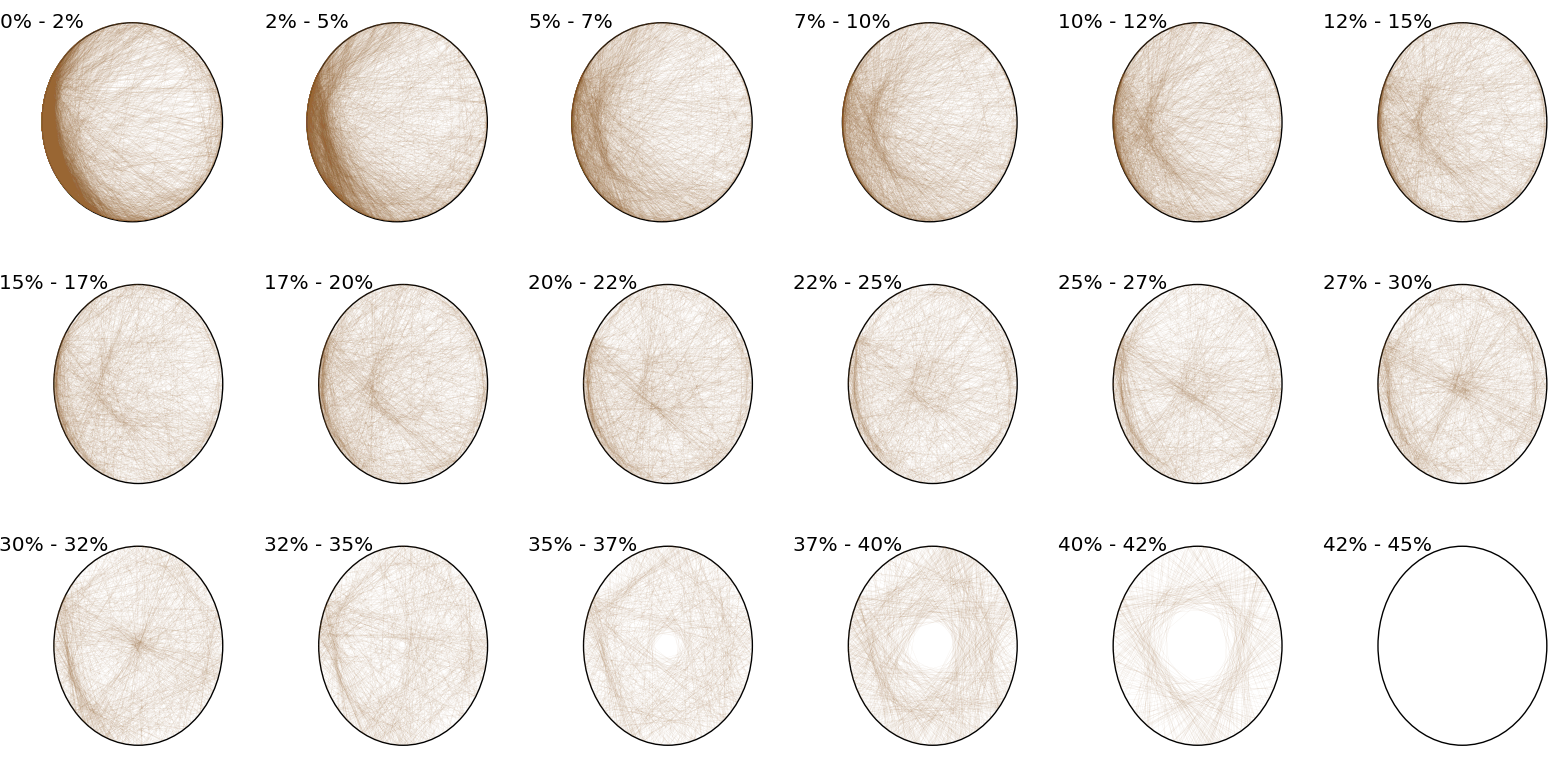

```mathematica
ClearAll["Global`*"]

rotate[n_]:=(alpha=2*Pi*fnfact[n];x=-Sin[alpha];y=Cos[alpha];{x,y});
fnfact[n_]:=n/(7^(Floor[Log[7,n]]+1)-7^Floor[Log[7,n]]);
intersectLines[line1_,line2_]:=(
a11=line1[[1,2]]-line1[[2,2]];a12=line1[[2,1]]-line1[[1,1]];det1=Det[line1];a21=line2[[1,2]]-line2[[2,2]];a22=line2[[2,1]]-line2[[1,1]];det2=Det[line2];detx=Det[{{a12,det1},{a22,det2}}];dety=Det[{{det1,a11},{det2,a21}}];det=Det[{{a11,a12},{a21,a22}}];If[det>0,{detx/det,dety/det},{0,0}]);

getTriangleLines[row_]:= (
pointA=rotate[Abs[row[[1]]]];
pointB=rotate[Abs[row[[2]]]];
pointC=rotate[Abs[row[[3]]]];
Line[{pointA,pointB,pointC,pointA}]
);

getPercentageArea[row_]:= (
pointA=rotate[Abs[row[[1]]]];
pointB=rotate[Abs[row[[2]]]];
pointC=rotate[Abs[row[[3]]]];
Area[Triangle[{pointA,pointB,pointC}]]/Area[Disk[]]
);

isInArea[value_, min_,max_]:=(value≥min&&value≤max);

csv=Import["C:/Users/esultano/git/pedal_curves/mathematica/datasets/313.csv", "Table"];
csv=Map[Function[{row},{row[[2]],row[[3]],row[[4]]}],csv];
csv=Select[csv,Function[{row},row[[1]]!=0&&row[[2]]!=0&&row[[3]]!=0]];
csv=Select[csv,Function[{row},Abs[row[[1]]]>7&&Abs[row[[2]]]>7&&Abs[row[[3]]]>7]];
csv=csv[[1;;10000]];
triangleLines=Map[getTriangleLines, csv];

plotPercentageRange[triangles_, from_, to_]:= (
filteredTriangles=Select[triangles, Function[t,isInArea[getPercentageArea[t],from,to]]];
lines=Map[getTriangleLines, filteredTriangles];
Graphics[{Text[Style[ToString[Floor[from*100]]<> "% - " <> ToString[Floor[to*100]]<> "%",Black, FontSize->20],{-1,1}], Circle[],Brown,Opacity[0.25],Thickness[0.0001],lines,PlotRange->{{-1,1},{-1,1}},AspectRatio->1}]
);

start=0.0;
stop=0.45;
step=0.025;

plots=Table[plotPercentageRange[csv, n,n+step],{n,start,stop,step}];

GraphicsGrid[{plots[[1;;6]],plots[[7;;12]],plots[[13;;18]]}, ImageSize->2000]
```